```mathematica
(*** Nullclines ***)
(* parameters taken from Parameters_SpatialGRN.xls/Sheet3 *)
```

```mathematica
(* Toggle Switch *)
f[x_,y_]:=gA*(B0A^nBA/(B0A^nBA+y^nBA)+(λBA*y^nBA)/(B0A^nBA+y^nBA))-γA*x;
g[x_,y_] := gB*(A0B^nAB/(A0B^nAB+x^nAB)+(λAB*x^nAB)/(A0B^nAB+x^nAB))-γB*y;
```

{{x→18.3281,y→2.00028},{x→-2.72619,y→-2.85724}}

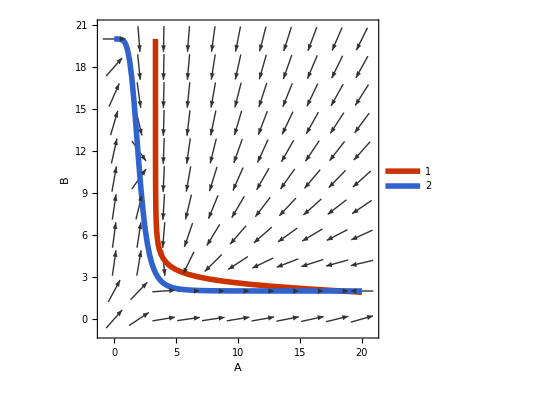

```mathematica
(* TS - Regime I (monostable parameter regime of) Bistable Parameter Set 1 *)
gA=10; gB=10; (* production rates *)
γA=0.3; γB=0.5; (* degradation rates *)
B0A=2; A0B=2; (* Threshold *)
nBA=5; nAB=5; (* Hill-coefficient *)
λBA=0.1;λAB=0.1;
S=NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals]
vp=VectorPlot[{f[x,y],g[x,y]},{x,0,20},{y,0,20},VectorPoints->11,VectorStyle->{GrayLevel[0.2]},VectorScale->{0.065,0.9,None}];cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,0,20},{y,0,20},PlotTheme-> "Web",ContourStyle->Directive[AbsoluteThickness[4]],Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,10],Axes-> True,BoundaryStyle->Black];
(*ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals];*)
Show[vp,cp,FrameLabel->{{HoldForm[B],None},{HoldForm[A],None}},PlotLabel->None,LabelStyle->{20,GrayLevel[0],Bold},Axes->True,AxesStyle->Black]
```